# Walker’s Problem Set 8

## Chapter 20

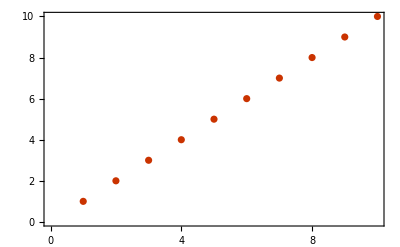

```mathematica
ListPlot[Range[10],PlotTheme->"Web"]
```

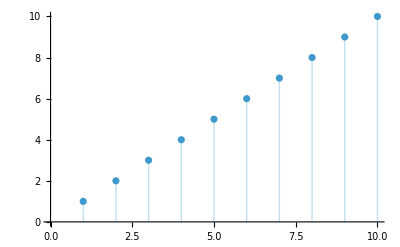

```mathematica
ListPlot[Range[10],Filling->Axis]
```

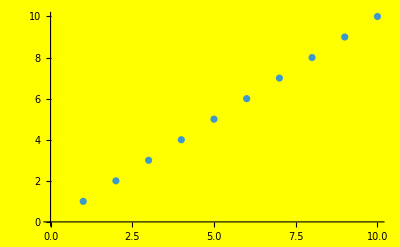

```mathematica
ListPlot[Range[10],Background->Yellow]
```

```mathematica
GeoListPlot[,GeoRange->All]
```

-Graphics-

```mathematica
GeoListPlot[,GeoRange->]
```

-Graphics-

```mathematica
GeoImage[,"ReliefMap"]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country","France"], Entity["Country","Finland"], Entity["Country","Greece"]},GeoLabels->True]
```

-Graphics-

```mathematica
GeoListPlot[EntityClass["University","TheIvyLeague"],GeoLabels->True]
```

-Graphics-

```mathematica
Style[Grid[Table[x*y,{x,12},{y,12}],Background->Black],White]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Disk[],ImageSize->RandomInteger[40]],100]
```

```mathematica
Table[Graphics[RegularPolygon[5],ImageSize->30,AspectRatio->n],{n,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Grid[Table[RandomColor[],10,10],Frame->All]
```

RGBColor[0.6261848881549461, 0.2652710225026198, 0.18780860205602656] | RGBColor[0.25165288617092396, 0.34277015099627905, 0.560270751801921] | RGBColor[0.8586097226263254, 0.39376662339434776, 0.2706495155522395] | RGBColor[0.3507407067766699, 0.844062168129468, 0.030465033461319235] | RGBColor[0.8174669967092287, 0.24398639870491623, 0.27841203228376044] | RGBColor[0.39329760714780293, 0.2145312188971369, 0.32521344926740015] | RGBColor[0.23719046589794224, 0.19437690049559353, 0.17737789676762272] | RGBColor[0.14456922393163074, 0.6342023517378699, 0.4026090433915801] | RGBColor[0.36375606654922676, 0.6198701658209953, 0.7143682453696005] | RGBColor[0.3137849465086149, 0.33226623847115166, 0.519750136919187]
RGBColor[0.22016132043762937, 0.09775229115815187, 0.27033999650324825] | RGBColor[0.6861228597156668, 0.40851241469468147, 0.8901574621736652] | RGBColor[0.960537258689679, 0.0996682573184533, 0.36533053949449834] | RGBColor[0.4043186544991544, 0.8861554309788393, 0.5431034989340973] | RGBColor[0.6439983155149855, 0.3677624482549784, 0.18099815597919355] | RGBColor[0.2455667111582227, 0.658931245909097, 0.27154678704398116] | RGBColor[0.574285757752665, 0.9103922846656232, 0.10248033018407443] | RGBColor[0.32287302779065175, 0.027668745867791777, 0.8454678063805181] | RGBColor[0.009348152931582199, 0.945144634052488, 0.8498204176102833] | RGBColor[0.14028368028923133, 0.7984358194871775, 0.9438574213534954]
RGBColor[0.6544936478731327, 0.8071147325594035, 0.48896588554932174] | RGBColor[0.09829313230334957, 0.6638938127711789, 0.37253390503818107] | RGBColor[0.467101677659002, 0.7416665577572712, 0.0967542751749233] | RGBColor[0.49329442428715664, 0.7444727797063051, 0.8023908604588279] | RGBColor[0.376470271455839, 0.8812951417533543, 0.3109129077497015] | RGBColor[0.5971387609478527, 0.4732608963843803, 0.3189486137166151] | RGBColor[0.9963479999766853, 0.6324609811911843, 0.4523853620478733] | RGBColor[0.35900536748961764, 0.4025399769639284, 0.0014913272224879037] | RGBColor[0.1759451863015673, 0.233482109619213, 0.7434574189740901] | RGBColor[0.9830689608027274, 0.9199667618997698, 0.8879363361236159]
RGBColor[0.06480304382198754, 0.1782793339879778, 0.8271104453622424] | RGBColor[0.1499885978728419, 0.2350273333545363, 0.6975405525174874] | RGBColor[0.9870779468088755, 0.12975143663644828, 0.07059756445831189] | RGBColor[0.20832776784648144, 0.10985717069792433, 0.7969295527750744] | RGBColor[0.40299438006482124, 0.2693066637330277, 0.2401021849762226] | RGBColor[0.3327194493465262, 0.7579185137710849, 0.7175290137558146] | RGBColor[0.10158688234165059, 0.5424717061246449, 0.5544854387609959] | RGBColor[0.28402657115962837, 0.3148805970065318, 0.08460142134854554] | RGBColor[0.4762018125989804, 0.7783448300121705, 0.7118390110461883] | RGBColor[0.4486651206839276, 0.7163603372289731, 0.15096652099926966]
RGBColor[0.2407476423820969, 0.11686400592427293, 0.4631942211843083] | RGBColor[0.5572927054870258, 0.5597780673897024, 0.40131832911207876] | RGBColor[0.029031985409763816, 0.40580838802806496, 0.9744230118779948] | RGBColor[0.6771503491361546, 0.41362263989958215, 0.18936492997062904] | RGBColor[0.17726034128422508, 0.2972938672308454, 0.9616998641257515] | RGBColor[0.7537842753004693, 0.8779143567557943, 0.5732301711488492] | RGBColor[0.40335203756204807, 0.21503882287419818, 0.7628888912275695] | RGBColor[0.23932149969502636, 0.1024466544293281, 0.004099129410904068] | RGBColor[0.8633087246081406, 0.6435415494709757, 0.9776844065909227] | RGBColor[0.7721725184200185, 0.6821487043096417, 0.43070254956519616]
RGBColor[0.6632477224162725, 0.6599218011561485, 0.23938291732890904] | RGBColor[0.41436863797577184, 0.7769192843443051, 0.7818189389200791] | RGBColor[0.38694935519143536, 0.7884947092214918, 0.6899649998503306] | RGBColor[0.013465173547721365, 0.19539831918392303, 0.38592434456260394] | RGBColor[0.8135347829169017, 0.8623092707720477, 0.49630285570048027] | RGBColor[0.7505115408030665, 0.9930766309065011, 0.9087876813188909] | RGBColor[0.5598521221777382, 0.21605380382166373, 0.2854948855832493] | RGBColor[0.45542788861529204, 0.15205572723043903, 0.6413801659399727] | RGBColor[0.5528045047706207, 0.19689004038114, 0.6402492790182521] | RGBColor[0.018037247064248696, 0.6112977907649764, 0.8907875183626504]
RGBColor[0.47878549219910194, 0.31750992129471967, 0.9138518219806528] | RGBColor[0.412807171708617, 0.22273131381033728, 0.7960814677467931] | RGBColor[0.11643208797442162, 0.09125005301628053, 0.19866270347875137] | RGBColor[0.9236043823385927, 0.39172552549257444, 0.21188416437943314] | RGBColor[0.37894866349932, 0.50911037707368, 0.64195397852377] | RGBColor[0.4288271498308147, 0.17491712646224133, 0.5505978776385207] | RGBColor[0.15619115010232498, 0.9884265103303689, 0.4695919740927281] | RGBColor[0.9327817028199292, 0.8679266275120874, 0.4683690964371583] | RGBColor[0.004790693923945488, 0.3129930909608778, 0.33567171705218835] | RGBColor[0.6894140294639393, 0.20473515215122506, 0.7245122901016763]
RGBColor[0.4888162736120425, 0.047158438709247186, 0.48611306736787463] | RGBColor[0.41451051829811125, 0.8937425235980234, 0.705400778963154] | RGBColor[0.9742976615436676, 0.6397207827342501, 0.016331948910881966] | RGBColor[0.8941613871609135, 0.2725142166367116, 0.30474284506602056] | RGBColor[0.5824745446929847, 0.6312647273780798, 0.8602743621137772] | RGBColor[0.6596658713144683, 0.8700512620825887, 0.14232309031954204] | RGBColor[0.28137829536378267, 0.7050242508783464, 0.07422267975803853] | RGBColor[0.8805638692362159, 0.017394761865489494, 0.701333423784908] | RGBColor[0.07069218543770894, 0.5995851852965546, 0.307874616056633] | RGBColor[0.31056138684843604, 0.003535428799463114, 0.39480341808055086]
RGBColor[0.5775421417236573, 0.7620537749403744, 0.4899876292689478] | RGBColor[0.3131133901418086, 0.4456255466573109, 0.2531030828766514] | RGBColor[0.5693303218799957, 0.30155904342006323, 0.1929588113602878] | RGBColor[0.44844537555925124, 0.0821162878036783, 0.5323311260671981] | RGBColor[0.018383352028186195, 0.5819323448918854, 0.3969120089511946] | RGBColor[0.34143253627435666, 0.29122148520830704, 0.7280785505555931] | RGBColor[0.5012438404255595, 0.7186411956164385, 0.5408274931454882] | RGBColor[0.3291452697560646, 0.5230819039711001, 0.016418545952280095] | RGBColor[0.7339181862255022, 0.4674014567959588, 0.9257020004088321] | RGBColor[0.4631575361369351, 0.6354455337458198, 0.9935948634517995]
RGBColor[0.879968288474763, 0.8705303116063279, 0.1609335712995712] | RGBColor[0.3900080191432642, 0.652275092762207, 0.8335194682153266] | RGBColor[0.12535737255313784, 0.34138667154728375, 0.3041527989882009] | RGBColor[0.9606433129503484, 0.3981055093977479, 0.32907856319405826] | RGBColor[0.20980449399756962, 0.9439367452382608, 0.5096345260492949] | RGBColor[0.016780908824846286, 0.10619373990334369, 0.6974419212928267] | RGBColor[0.09710323541142496, 0.3821747213255242, 0.060529312120694456] | RGBColor[0.24311156578015458, 0.10106933001471541, 0.6431078820266252] | RGBColor[0.3775576331237158, 0.7138269524169747, 0.29010458299866504] | RGBColor[0.6619018336346292, 0.23995800524984112, 0.966485686184164]

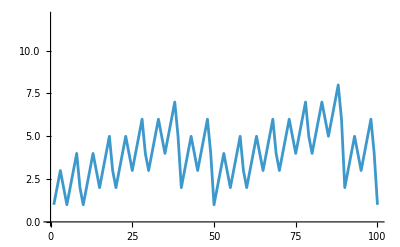

```mathematica
ListLinePlot[StringLength[RomanNumeral[Range[100]]],PlotRange->Max[StringLength[RomanNumeral[Range[1000]]]]]
```

## Chapter 21

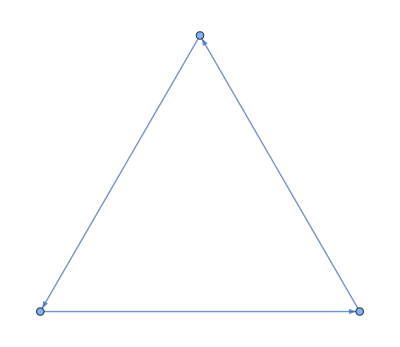

```mathematica
Graph[{1->2,2->3,3->1}]
```

```mathematica
Graph[Flatten[Table[x->y,{x,4},{y,4}]]]
```

-Graphics-

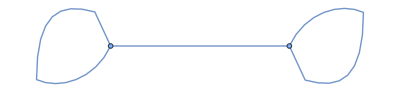
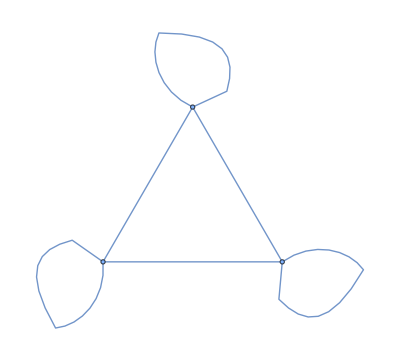
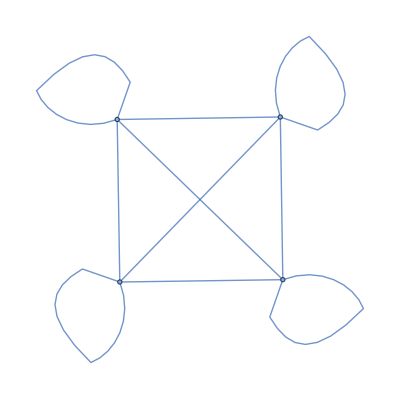
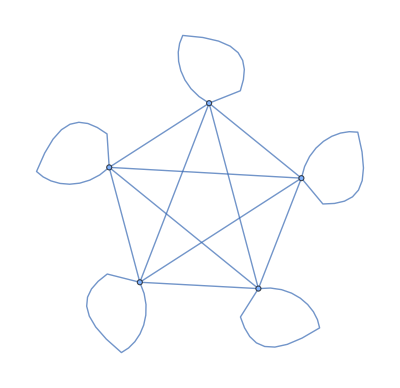
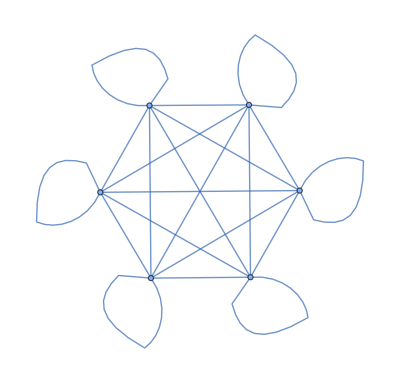
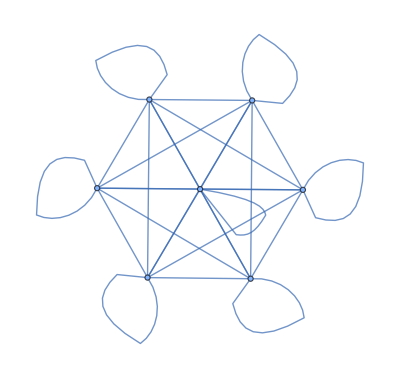
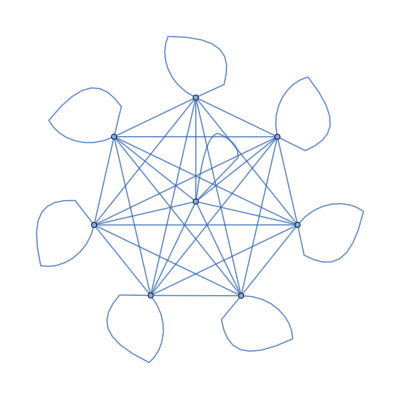
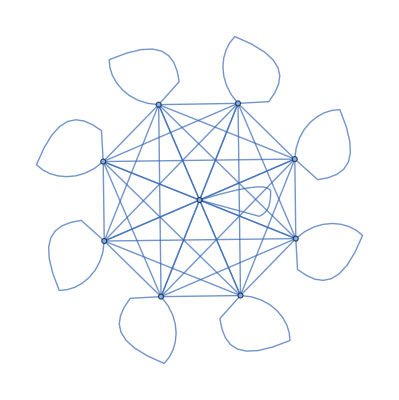

```mathematica
Table[UndirectedGraph[Flatten[Table[x->y,{x,n},{y,n}]]],{n,2,10,1}]
```

```mathematica
Flatten[Table[Range[2],3]]
```

{1,2,1,2,1,2}

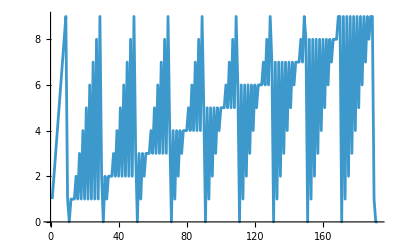

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

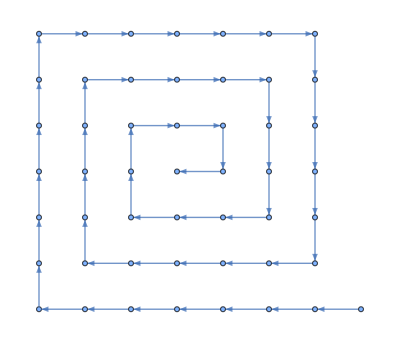

```mathematica
Graph[Flatten[Table[n->n+1,{n,49}]]]
```

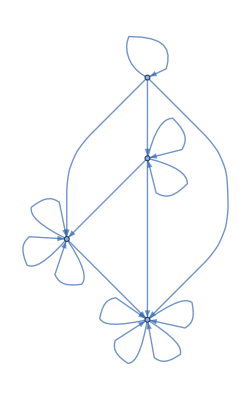

```mathematica
Graph[Flatten[Table[n->Max[n,j],{n,4},{j,4}]]]
```

```mathematica
Graph[Flatten[Table[i->(j-i),{i,5},{j,5}]]]
```

-Graphics-

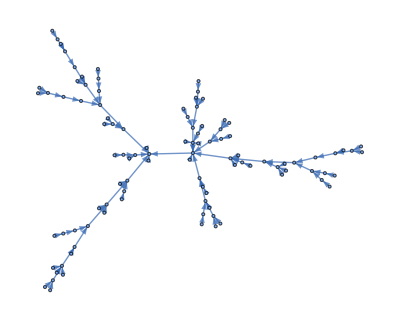

```mathematica
Graph[Flatten[Table[n->RandomInteger[n-1],{n,100}]]]
```

```mathematica
Graph[Flatten[Table[Table[n->RandomInteger[n-1],{n,100}],2]]]
```

-Graphics-

```mathematica
Grid[Table[FindShortestPath[Graph[{1->2,2->3,3->4,4->1,3->1,2->2}],a,b],{a,4},{b,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

## Chapter 22

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
ImageIdentify[EntityValue[,"Image"]]
```

tiger

```mathematica
ImageIdentify[Table[Blur[EntityValue[,"Image"],n],{n,1,5}]]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
Nearest[Table[RandomInteger[1000],20],100,3]
```

{96,66,167}

```mathematica
Nearest[Table[RandomColor[],10],Red,5]
```

{RGBColor[0.829281880264561, 0.1784048629100523, 0.5241120012015776],RGBColor[0.45269267878269215, 0.26377621397696815, 0.19338508218544703],RGBColor[0.6772780920083432, 0.7304471811753879, 0.6558715375374908],RGBColor[0.6966624380052835, 0.8516786234779565, 0.1232889518579321],RGBColor[0.35520979044781487, 0.5069719067779523, 0.6210943286030881]}

```mathematica
Nearest[Table[n^2,{n,2000}],2000]
```

{2025}

```mathematica
Nearest[EntityValue[EntityList[],"Flag"],EntityValue[,"Flag"],3]
```

{-Graphics-,-Graphics-,-Graphics-}

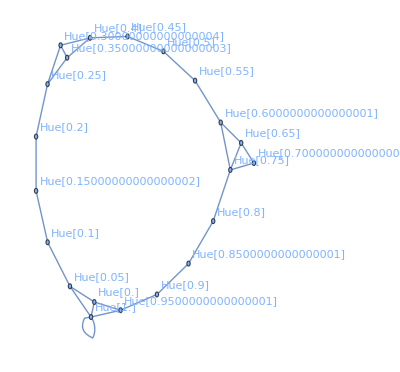

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,.05}],2,VertexLabels->All]
```

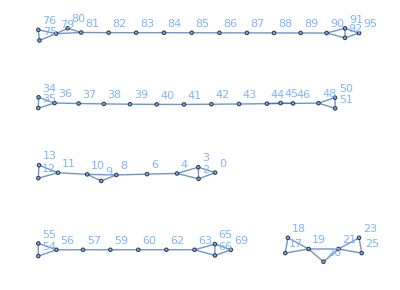

```mathematica
NearestNeighborGraph[Table[RandomInteger[100],100],2,VertexLabels->All]
```


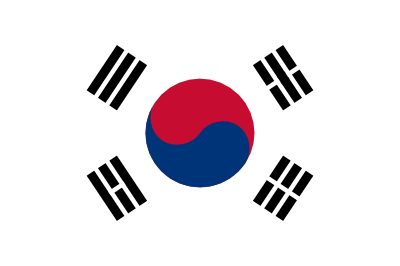
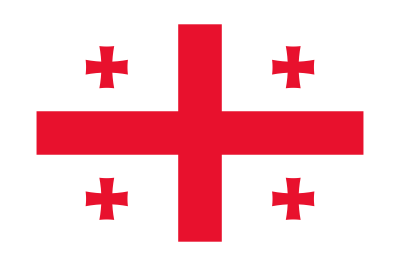
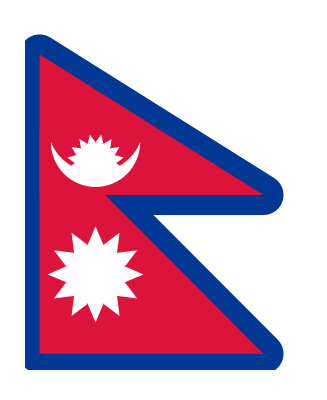
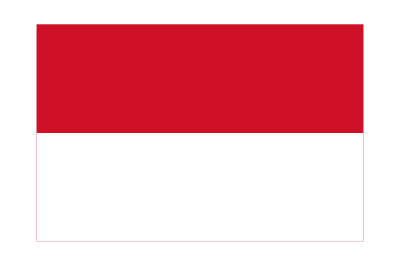
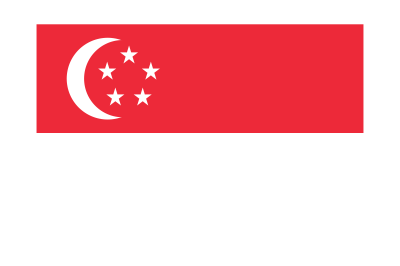
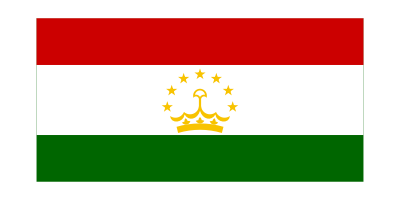
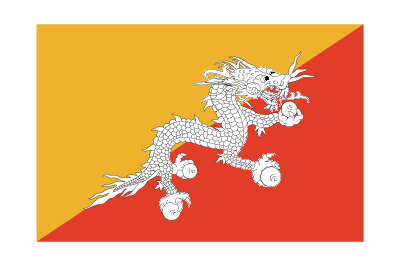
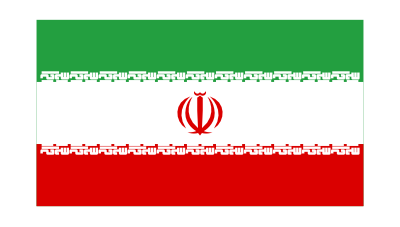

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[EntityValue[EntityList[],"Flag"]]
```

```mathematica
NearestNeighborGraph[Table[Rasterize[Style[Alphabet[][[n]],20]],{n,26}],2,VertexLabels->All]
```

-Graphics-

```mathematica
TextRecognize[Table[EdgeDetect[Rasterize[Style["programing",n]]],{n,10,20,1}]]
```

{programing,programing,programing,programing,programing,programing,programi
ing,programing,programing,programing,programing}

```mathematica
Dendrogram[Table[Rasterize[Alphabet[][[n]]],{n,10}]]
```

-Graphics-

```mathematica
FeatureSpacePlot[Table[Rasterize[ToUpperCase[Alphabet[][[n]]]],{n,26}]]
```

-Graphics-